# Trigonometria applicata alle distanze

Progetto d’esame : Matematica Computazionale & Calcolo Numerico e Software Didattico

REALIZZATO DA:

# -Graphics- -Graphics- -Graphics- -Graphics- Anno Accademico 2017/2018

-Graphics-

Prima di iniziare

```mathematica
Button["Carica Package",
	SetDirectory[NotebookDirectory[]];<<Package.m; 
	CreateDialog[
		Column[{
			StringForm["Il package è stato caricato correttamente\n"],
			(* pulsante di chiusura del modale *)
			DefaultButton[Style["Chiudi",FontSize -> 18],
				DialogReturn[] (* chiude il dialog *)
			]
		},ItemSize->20], (* end Column della dialog*)
		Modal->True,  (* indica di aprire il dialog come schermata modale (pop-up) *)
		NotebookEventActions->{"WindowClose":>(DialogReturn[])} (* evento di chiusura del dialog *)
	](* end DIALOG *),
BaseStyle->{Red,40}
]
```

Carica Package

Ci siamo quasi : manca solo un ultimo passaggio

1.	Vai sul menu “Evaluation”                                      -Graphics-


2.      E clicca su “Evaluate Notebook”						-Graphics-

-Graphics-Iniziamo

# Da cosa vuoi iniziare? -Graphics- -Graphics- -Graphics-

-Graphics--Graphics-

# -Graphics-

Durante le vacanze, Lorenzo va a Parigi. 
Di fronte alla maestosità della tour Eiffel si chiede : 
"Ma quanto sarà alta?".
Capendo di non poter srotolare un metro da sarta lungo più di  cento metri, 
si domanda se esista un modo più semplice di trovare una soluzione. 
Noi siamo qui per mostrarvelo. | -Graphics-

-Graphics-

## Cos’è la trigonometria?

La trigonometria è quella parte della matematica che studia i triangoli e le funzioni circolari. 
La sua utilità è quella di fornire informazioni sui triangoli a partire dai loro angoli e vanta numerose applicazioni nel mondo reale.

-Graphics-

## Cos’è un angolo?

Un angolo è la parte di piano compresa  tra due semirette aventi origine comune. 
  • Se le due semirette sono coincidenti:
  	- se l’angolo è formato dalla sola semiretta: angolo nullo 
       - se l’angolo è formato da tutti i punti del piano: angolo giro
  • Se le semirette sono l’una il prolungamento dell’altra: angolo piatto. 
  • Se due semirette incontrandosi  formano quattro angoli congruenti: angolo retto.

```mathematica
TipoAngolo[]
ThGradRad[]
```

## Angoli Orientati

Conviene collegare l'idea di angolo a quella di rotazione di uno dei due lati.
Questa rotazione può avvenire in verso:

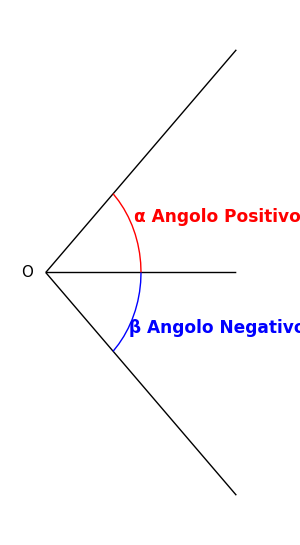
-Graphics-	Conviene collegare l'idea di angolo 
a quella di rotazione di uno dei due lati.
Questa rotazione può avvenire in verso:

- Antiorario, e diciamo che è positivo;
- Orario, e diciamo che è negativo.

```mathematica
AngoloOrientato[]
```

## Circonferenza Goniometrica

D’ora in avanti chiameremo goniometrica la circonferenza con centro nell’origine e raggio 1. 
La sua equazione è: x^2+ y^2 = 1

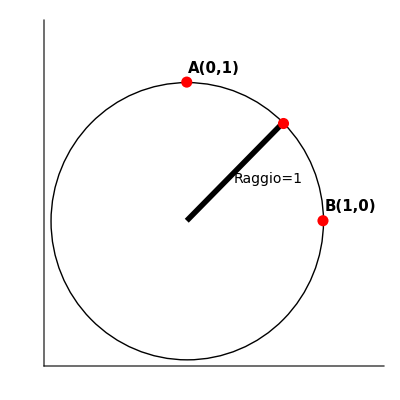

```mathematica
DisegnaCirconferenzaInit[]
```

## Seno e Coseno

Prendiamo la circonferenza goniometrica e un angolo orientato α, chiamiamo:
    - Coseno  di α, e indichiamo con cos(α), l’ascissa del punto P
    - Seno  di α, e indichiamo con sin(α), l'ordinata del punto P

```mathematica
DisegnaCirconferenza[]
```

## Prima relazione fondamentale

Abbiamo visto che l’equazione della circonferenza goniometrica è x^2+ y^2 = 1 dove x e y sono rispettivamente l’ascissa (coseno) e l’ordinata (seno) di un punto appartenente alla circonferenza. 
Dunque cos^2(α) + sin^2(α) = 1, ∀α.

```mathematica
GraficoPrimaRelazione[]
```

## Tangente

Definiamo la terza funzione goniometrica : la tangente. 
Preso un angolo orientato α, la sua tangente è definita come il rapporto tra sin(α) e cos (α).

tan(α ) = (sin(α))/(cos(α))

Il denominatore deve essere diverso da 0, quindi α≠π/2,(3π)/2

```mathematica
GraficoTangente[]
```

OSSERVAZIONE: per definizione di seno e coseno, la tangente di un angolo α è il rapporto tra l'ordinata e l'ascissa del punto associato

## Angoli Associati

Anzichè memorizzare i valori del seno e del coseno di ogni angolo, vediamo come è possibile ricavare tali valori attaverso l’utilizzo dei seguenti quattro angoli noti:

0°

```mathematica
AngoliAssociati0[]
```

π/6 ~ 30°

```mathematica
AngoliAssociati30[]
```

π/4 ~ 45°

```mathematica
AngoliAssociati45[]
```

π/3 ~ 60°

```mathematica
AngoliAssociati60[]
```

## Triangoli

Consideriamo un triangolo rettangolo qualsiasi. Vogliamo ricavare le sue proprietà utilizzando ciò che sappiamo della goniometria. 
Il triangolo ABC è retto in C. Ora tracciamo la circonferenza goniometrica di centro A.

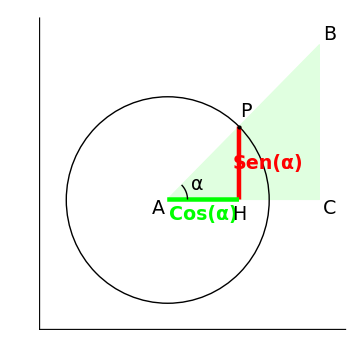
I triangoli ABC e APH sono simili,
perciò il rapporto tra i lati
è costante, da cui ricaviamo che:
BC : AB = PH : AP
AC : AB = AH : AP
e poichè:
AP = 1
PH = Sen(α)
AH = Cos(α)
vale
BC = Sen(α) AB   AC = Cos(α) AB		-Graphics-

```mathematica
ThTriangoloProiezione[]
```

Cosa succede se AB è minore di 1 ?
I triangoli restano simili e quindi la proiezione è invariata.

Possiamo riformularle in questo modo:

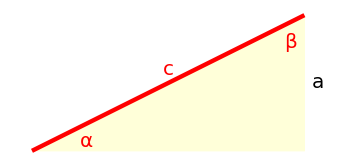
-Graphics-		Cateto = Ipotenusa * seno dell'angolo opposto
a = c * Sen(α)


Cateto = Ipotenusa * coseno dell'angolo acuto adiacente
a = c * Cos(β)

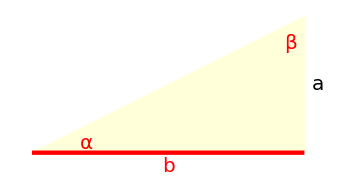
-Graphics-		Cateto = altroCateto * Tangente angolo
a = b * Tan(α)

```mathematica
ThTriangoliUno[] 
ThTriangoliDue[]
```

Molto importante è quest'ultima formula perchè ci servirà per determinare l'altezza di una torre.

## Teorema del seno

In un triangolo le misure dei lati sono proporzionali ai seni degli angoli opposti:

-Graphics-                    -Graphics-

## Teorema del coseno

In un triangolo di lati a, b, c, vale la seguente formula:

-Graphics-		-Graphics-

-Graphics--Graphics-

# -Graphics-

## Individua le coordinate

Individua le coordinate x ed y del punto rosso situato nel piano cartesiano:

```mathematica
EsCoordinate[]
```

## Distanza tra due Punti

```mathematica
EsDistanze[]
```

## Converti Grad ~ Rad

```mathematica
EsRadiantDegree[]
```

## Calcola Seno

```mathematica
EsSin[]
```

## Calcola Coseno

```mathematica
EsCos[]
```

-Graphics- -Graphics-

# -Graphics-

Ora abbiamo gli strumenti per calcolare alcune misure tra cui l’altezza di una torre oppure la distanza che intercorre tra uno o due punti inaccessibili.

## Altezza di una torre

```mathematica
AltezzaTorre[]
```

Lorenzo, dopo questa lettura, ha avuto un'idea
su come calcolare facilmente l'altezza della tour Eiffel.
Procede in questo modo: 
misura la sua distanza dalla base della torre
e approssima l'angolo α (vedi ottante).
Osserva che si forma un triangolo rettangolo
e può quindi usare la proprietà della tangente.

## Distanza di un punto non accessibile

```mathematica
DistancePointsApplication[]
```

Supponiamo di voler calcolare la distanza fra due punti B e C:
io mi trovo in C ma non posso raggiungere B perché è al di lá del fiume.
Possiamo spostarci in un punto A e calcolare la distanza AC
ed inoltre gli angoli CAB=α e ACB=β.


Abbiamo quindi il triangolo ABC in cui conosciamo due angoli ed il lato compreso,
quindi per risolvere il triangolo possiamo calcolare il terzo angolo ricordando che
la somma degli angoli interni di un triangolo è un angolo piatto.

γ = 180° - α - β

E poi applicare il teorema dei seni:  

 AC/(Sen(γ)) = BC/(Sen(α))

Ottenendo quindi:

 BC = (AC Sen(α))/(Sen(γ))
Esempio

AC = 20m
CAB = α = 45°
BCA = β = 90°	
Quanto misura BC?
 
12m18m21m28m

## Distanza di due punti non accessibili

```mathematica
puntiInaccessibili[]
```

-Graphics--Graphics-